NAME : PARTH KUMAR SINGH
COLLEGE ROLL NO.: 2232139
UNIVERSITY ROLL NO.: 22036563034
COURSE : B.Sc. (Hons.) Mathematics/Year3/Complex Analysis
SECTION : A

PRACTICAL 9 : Plot the line segment joining the two specified end points. And find the integral of the given function over that specified line segment.

1. f (z) = z, z0 = -1 + 3 ⅈ, z1 = 2 + ⅈ

```mathematica
Integrate[z, {z, -1 + 3 ⅈ, 2 + ⅈ}]
```

11/2+5 ⅈ

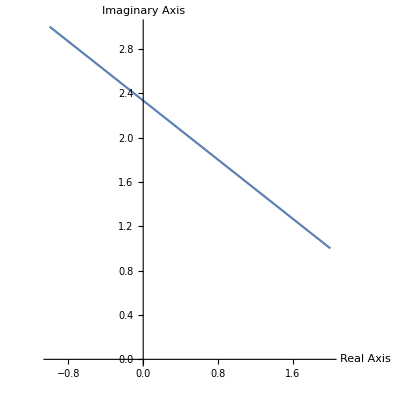

The value of the integration is

 C z ⅆz = 11/2+5 ⅈ

where C: c[t] = -1+ⅈ (3-2 t)+3 t, for 0 ≤ t ≤ 1.

```mathematica
ClearAll;
f[z_] = z ; 
z0 = -1 + 3 ⅈ; 
z1 = 2 + ⅈ; 
x0 = Re[z0]; y0 = Im[z0]; 
x1 = Re[z1]; y1 = Im[z1];
L[t_] = x0 + (x1 - x0) t + ⅈ (y0 + (y1 - y0) t); 
w[t_] = f[L[t]] * L'[t];
W1 = Integrate[w[t],{t, 0,1} ];

ParametricPlot[{Re[L[t]], Im[L[t]]}, {t, 0, 1}, Axes -> True, AxesOrigin -> {0, 0}, AxesLabel -> {"Real Axis", "Imaginary Axis"}] 

Print["The value of the integration is"]; 
Print[" C ", f[z], " ⅆz = ", W1]; 
Print["where C: c[t] = ", L[t], ", for 0 ≤ t ≤ 1."];
```

2.  f (z) = z, z0 = -1 - ⅈ, z1 = 3 + ⅈ

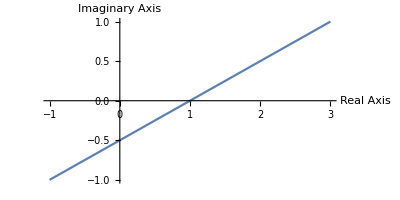

The value of the integration is

 C z ⅆz = 4+2 ⅈ

where C: c[t] = -1+4 t+ⅈ (-1+2 t), for 0 ≤ t ≤ 1.

```mathematica
f[z_] = z ; z0 = -1 - ⅈ; 
z1 = 3 + ⅈ; 

x0 = Re[z0]; y0 = Im[z0]; 
x1 = Re[z1]; y1 = Im[z1]; 

L[t_] = x0 + (x1 - x0) t + ⅈ (y0 + (y1 - y0) t); 
w[t_] = ComplexExpand[f[L[t]] * L'[t]];
W1 = Integrate[w[t], {t, 0, 1}] ; 

ParametricPlot[{Re[L[t]], Im[L[t]]}, {t, 0, 1}, Axes -> True, 
AxesOrigin -> {0, 0}, AxesLabel -> {"Real Axis", "Imaginary Axis"}]

Print["The value of the integration is"];
Print[" C ", f[z], " ⅆz = ", W1]; 
Print["where C: c[t] = ", L[t], ", for 0 ≤ t ≤ 1."];
```

3: f (z) = sin z, z0 = -1 + ⅈ, z1 = 2 - ⅈ

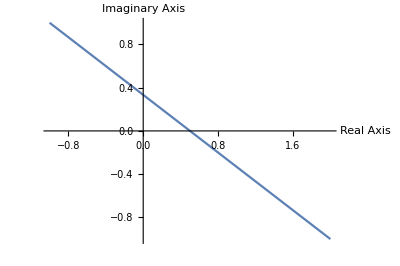

The value of the integration is

 C Sin[z] ⅆz = Cosh[1+ⅈ]-Cosh[1+2 ⅈ]

where C: c[t] = -1+ⅈ (1-2 t)+3 t, for 0 ≤ t ≤ 1.

```mathematica
f[z_] = Sin[z] ; 
z0 = -1 + ⅈ; 
z1 = 2- ⅈ; 

x0 = Re[z0]; y0 = Im[z0]; 
x1 = Re[z1]; y1 = Im[z1]; 

L[t_] = x0 + (x1 - x0) t + ⅈ (y0 + (y1 - y0) t); 
w[t_] = ComplexExpand[f[L[t]] * L'[t]];
W1 = Integrate[w[t], {t, 0, 1}] ; 

ParametricPlot[{Re[L[t]], Im[L[t]]}, {t, 0, 1}, Axes -> True, 
AxesOrigin -> {0, 0}, AxesLabel -> {"Real Axis", "Imaginary Axis"}]

Print["The value of the integration is"];
Print[" C ", f[z], " ⅆz = ", W1]; 
Print["where C: c[t] = ", L[t], ", for 0 ≤ t ≤ 1."];
```

4 : f (z) = z, z0 = -1 +ⅈ, z1 = 2 - ⅈ

```mathematica
f[z_] = Conjugate[z] ; 
z0 = -1 + ⅈ; 
z1 = 2- ⅈ; 

x0 = Re[z0]; y0 = Im[z0]; 
x1 = Re[z1]; y1 = Im[z1]; 

L[t_] = x0 + (x1 - x0) t + ⅈ (y0 + (y1 - y0) t); 
w[t_] = ComplexExpand[f[L[t]] * L'[t]];
W1 = Integrate[w[t], {t, 0, 1}] ; 

ParametricPlot[{Re[L[t]], Im[L[t]]}, {t, 0, 1}, Axes -> True, 
AxesOrigin -> {0, 0}, AxesLabel -> {"Real Axis", "Imaginary Axis"}]

Print["The value of the integration is"];
Print[" C ", f[z] //TraditionalForm, " ⅆz = ", W1]; 
Print["where C: c[t] = ", L[t], ", for 0 ≤ t ≤ 1."];
```

-Graphics-

The value of the integration is

 C Conjugate[z] ⅆz = 3/2-ⅈ

where C: c[t] = -1+ⅈ (1-2 t)+3 t, for 0 ≤ t ≤ 1.